```mathematica
dim=8;
Clear[μ,η,y]
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x1*x3+y*x0*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
```

```mathematica
Simplify[SB[0],Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0]
```

{B[0]→2 A[0]+Log[(η √μ A[1]^2 A[3] A[5])/(((A[3]^4+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[5]^2) (1+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[3]^4 A[5]^2))^(1/8) ((η^2 A[1]^4+2 η μ A[1]^2 A[5]+A[5]^2) (η^2 A[1]^4 A[5]+A[3]^2 A[5]+η μ A[1]^2 (A[3]^2+A[5]^2)) (A[5]+η^2 A[1]^4 A[3]^2 A[5]+η μ A[1]^2 (1+A[3]^2 A[5]^2)))^(1/4))]}

```mathematica
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[SB[n],1],{n,0,5}]
```

{B[0]→2 A[0]+Log[(η √μ A[1]^2 A[3] A[5])/(((A[3]^4+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[5]^2) (1+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[3]^4 A[5]^2))^(1/8) ((η^2 A[1]^4+2 η μ A[1]^2 A[5]+A[5]^2) (η^2 A[1]^4 A[5]+A[3]^2 A[5]+η μ A[1]^2 (A[3]^2+A[5]^2)) (A[5]+η^2 A[1]^4 A[3]^2 A[5]+η μ A[1]^2 (1+A[3]^2 A[5]^2)))^(1/4))],B[1]→(A[1] A[2] √(η^2 A[1]^4 A[5]+A[3]^2 A[5]+η μ A[1]^2 (A[3]^2+A[5]^2)) ((A[3]^4+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[5]^2)/(A[3]^2 A[5]^2+η^4 A[1]^8 A[3]^2 A[5]^2+η^3 μ A[1]^6 A[5] (1+A[3]^4+2 A[3]^2 A[5]^2)+η μ A[1]^2 A[5] (2 A[3]^2+A[5]^2+A[3]^4 A[5]^2)+η^2 A[1]^4 ((1+A[3]^4) A[5]^2+μ^2 (A[5]^2+A[3]^4 A[5]^2+A[3]^2 (1+A[5]^4)))))^(1/4))/(η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+2 η μ A[1]^2 A[3]^2 A[5] (1+η^2 A[1]^4 A[5]^2)+2 η μ A[1]^2 A[3]^6 A[5] (1+η^2 A[1]^4 A[5]^2)+A[3]^4 (1+4 η^2 μ^2 A[1]^4 A[5]^2+η^4 A[1]^8 A[5]^4))^(1/8),B[2]→((μ^(-1+y) (A[3]^4+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[5]^2))/(1+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[3]^4 A[5]^2))^(1/8) ((μ^(1/2-y/2) (A[5]+η^2 A[1]^4 A[3]^2 A[5]+η μ A[1]^2 (1+A[3]^2 A[5]^2)))/(η^2 A[1]^4 A[5]+A[3]^2 A[5]+η μ A[1]^2 (A[3]^2+A[5]^2)))^(1/4),B[3]→(A[3] A[4] √(η^2 A[1]^4+2 η μ A[1]^2 A[5]+A[5]^2))/(η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+2 η μ A[1]^2 A[3]^2 A[5] (1+η^2 A[1]^4 A[5]^2)+2 η μ A[1]^2 A[3]^6 A[5] (1+η^2 A[1]^4 A[5]^2)+A[3]^4 (1+4 η^2 μ^2 A[1]^4 A[5]^2+η^4 A[1]^8 A[5]^4))^(1/4),B[4]→(μ^y (η^2 A[1]^4 A[5]+A[3]^2 A[5]+η μ A[1]^2 (A[3]^2+A[5]^2)) (A[5]+η^2 A[1]^4 A[3]^2 A[5]+η μ A[1]^2 (1+A[3]^2 A[5]^2)))/((η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+2 η μ A[1]^2 A[3]^2 A[5] (1+η^2 A[1]^4 A[5]^2)+2 η μ A[1]^2 A[3]^6 A[5] (1+η^2 A[1]^4 A[5]^2)+A[3]^4 (1+4 η^2 μ^2 A[1]^4 A[5]^2+η^4 A[1]^8 A[5]^4))^(1/4) √((η^2 A[1]^4+2 η μ A[1]^2 A[5]+A[5]^2) (A[3]^2 A[5]^2+η^4 A[1]^8 A[3]^2 A[5]^2+η^3 μ A[1]^6 A[5] (1+A[3]^4+2 A[3]^2 A[5]^2)+η μ A[1]^2 A[5] (2 A[3]^2+A[5]^2+A[3]^4 A[5]^2)+η^2 A[1]^4 ((1+A[3]^4) A[5]^2+μ^2 (A[5]^2+A[3]^4 A[5]^2+A[3]^2 (1+A[5]^4)))))),B[5]→((A[5]+η^2 A[1]^4 A[3]^2 A[5]+η μ A[1]^2 (1+A[3]^2 A[5]^2)) √((A[3]^4+2 η μ A[1]^2 A[3]^2 A[5]+η^2 A[1]^4 A[5]^2)/(A[3]^2 A[5]^2+η^4 A[1]^8 A[3]^2 A[5]^2+η^3 μ A[1]^6 A[5] (1+A[3]^4+2 A[3]^2 A[5]^2)+η μ A[1]^2 A[5] (2 A[3]^2+A[5]^2+A[3]^4 A[5]^2)+η^2 A[1]^4 ((1+A[3]^4) A[5]^2+μ^2 (A[5]^2+A[3]^4 A[5]^2+A[3]^2 (1+A[5]^4))))))/(η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+2 η μ A[1]^2 A[3]^2 A[5] (1+η^2 A[1]^4 A[5]^2)+2 η μ A[1]^2 A[3]^6 A[5] (1+η^2 A[1]^4 A[5]^2)+A[3]^4 (1+4 η^2 μ^2 A[1]^4 A[5]^2+η^4 A[1]^8 A[5]^4))^(1/4)}

```mathematica
(* Set up Initial values(SIC),Initial Step, RG steps, W, Z1, LnZ1, DLnZ1, and constants*)
Clear[μ,η,y]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->μ^(y),B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[D[(B[i]/.SBT),A[j]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
```

```mathematica
SIC
Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
dA0dμ
Table[D[A[i]/.SAT,η],{i,0,dim-1}]
dA0dη
```

{B[0]→0,B[1]→η,B[2]→η,B[3]→μ,B[4]→μ^y,B[5]→1}

{0,0,0,1,y μ^(-1+y),0,1,0}

{0,0,0,-4 μ,-4 y μ^y,0,-4 μ,0}

{0,1,1,0,0,0,0,1}

{0,-2 η,-2 η,0,0,0,0,-2 η}

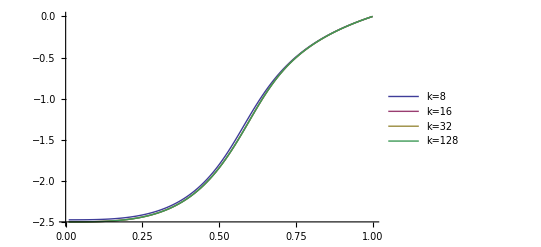

```mathematica
(***** Constants for IE: Internal Energy*****)
Clear[μ,η,y]
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
kVector={8,16,32,64};
(******* Internal Energy <e> *******)
Clear[μ,η,y];
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
η=1;
y=1;
η=0.998;
IE=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
μind=0;
Do[
kind=1;
μind++;
InitRGW;
For[i=3,i≤Max[kVector],++i,
RGW;
If[i==kVector[[kind]],
Part[Part[IE,kind],μind]=-1.0/(2^(i)+1)*(dA0dμ.Υ).(DLnZ1/.SAT);kind++,];
],
{μ,μmin,μmax,μinc}
];
ListLinePlot[Table[Table[{μVector[[i]],IE[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=16","k=32","k=128"},PlotStyle->Thick,AxesOrigin->{0,-2.5}]
```

```mathematica
IE[[4]]
```

{-2.5,-2.49998,-2.49992,-2.4998,-2.49961,-2.49933,-2.49892,-2.49838,-2.49767,-2.49677,-2.49566,-2.49432,-2.4927,-2.4908,-2.48857,-2.48598,-2.48301,-2.47962,-2.47577,-2.47143,-2.46657,-2.46113,-2.45508,-2.44837,-2.44096,-2.43281,-2.42385,-2.41405,-2.40333,-2.39166,-2.37896,-2.36517,-2.35022,-2.33406,-2.3166,-2.29777,-2.27749,-2.25568,-2.23226,-2.20714,-2.18023,-2.15144,-2.12068,-2.08787,-2.05291,-2.01572,-1.97624,-1.93438,-1.89011,-1.84338,-1.79419,-1.74256,-1.68856,-1.63228,-1.57388,-1.51359,-1.45169,-1.38853,-1.32452,-1.26014,-1.19589,-1.1323,-1.06988,-1.0091,-0.950363,-0.893975,-0.840156,-0.789023,-0.740608,-0.694873,-0.651727,-0.61104,-0.572663,-0.536438,-0.502205,-0.469808,-0.439102,-0.409949,-0.382227,-0.355821,-0.330631,-0.306565,-0.283541,-0.261484,-0.240329,-0.220015,-0.200487,-0.181695,-0.163593,-0.146139,-0.129296,-0.113026,-0.0972972,-0.0820793,-0.0673437,-0.0530645,-0.0392172,-0.0257792,-0.0127296,-0.0000485965}

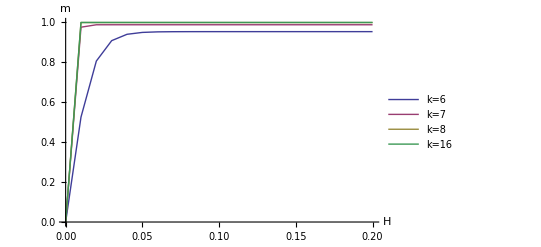

```mathematica
(***** Constants for magnetization: <m> vs H*****)
Clear[μ,η,y];
InitRGW;
y=0;
Hmin=0.0;
Hmax=0.2;
Hinc=0.01;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=Exp[-2*Hmin];
ηmin=Exp[-2*Hmax];
ηVector=Exp[-2*HVector];
kVector={6,8, 12,16};
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
μ=0.00001;
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η];
kind=1;
InitRGW;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[MagH,kind],i]=1.0/(2^j+1)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7", "k=8", "k=16"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m} ]
```

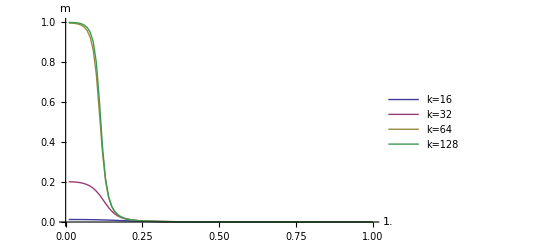

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η,y];
y=0.0;
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={8,12,16,18};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=0.9999;
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}, PlotRange->Full]
```

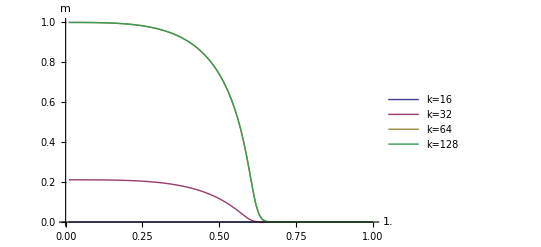

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η,y];
y=1;
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={16,32,64,128};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=0.9999999999;
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```